http://stackoverflow.com/questions/7954580/mathematica-plot-with-manipulate-shows-no-output

```mathematica
Clear[f, mu]
f[ x_, z_] = (x Sin[mu]+z Cos[mu])^2 
(* f[ x_, z_] = (x +z )^2  *)
Manipulate[ Plot3D[ f[x, z], {x, -10, 10}, {z, -10, 10}], {mu, 0, 2 π}] 
Plot3D[ f[x, z] /. mu -> 0, {x, -10, 10}, {z, -10, 10}]
```

(z Cos[mu]+x Sin[mu])^2

-Graphics3D-

x^2 Sin[mu]^2

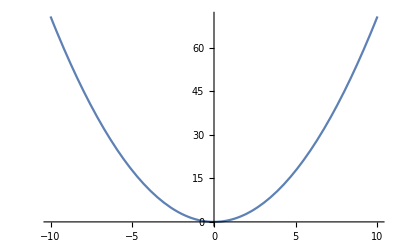

```mathematica
Clear[g, mu]
g[ x_] = (x Sin[mu])^2 
Manipulate[ Plot[ g[x], {x, -10, 10}], {{mu, 1}, 0, 2 π}] 
Manipulate[ Plot[ g[x], {x, -10, 10}, PlotRange -> {0, 70}], {{mu, 1}, 0, 2 π}] 
Plot[ g[x] /. mu -> 1, {x, -10, 10}]
```